# Inlämningsuppgift 1

## Uppgift 1

### Hitta lösningarna till polynomekvationen: 2/3 x^5-2/3 x^4-8 x^3+8 x^2+18x-18=0. Rita också grafen för polynomet och markera nollställen med en röd punkt.

Jag gör en funktion av polynomet.

```mathematica
f[x_]=((2/3)x^5)-((2/3)x^4)-(8x^3)+(8x^2)+18x-18
```

-18+18 x+8 x^2-8 x^3-(2 x^4)/3+(2 x^5)/3

Vi vet att det kommer att finnas fem lösningar i ekvationen. Vi behöver därför fem variabler där vi sparar lösningarna från ekvationen som vi får fram genom Solve.

```mathematica
{x1,x2,x3,x4,x5}=x/.Solve[f[x]==0,x]
```

{-3,1,3,-√3,√3}

Lösningarna är:  -3,1,3,-√3,√3. Dessa är sparade i x1,x2,x3,x4,x5.

Nedan ritar vi upp en graf för polynomet och markerar dess nollställen med röd punkt.

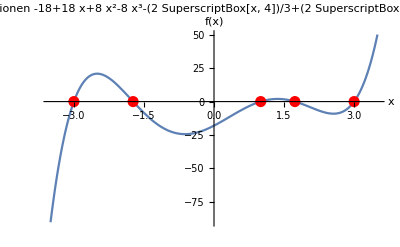

```mathematica
Plot[f[x],{x,-3.5,3.5},AxesLabel->{"x","f(x)"},PlotLabel->"Ekvationen -18+18 x+8 x^2-8 x^3-(2 SuperscriptBox[x, 4])/3+(2 SuperscriptBox[x, 5])/3=0",Epilog->{PointSize[0.02],Red,Point[{{x1,f[x1]},{x2,f[x2]},{x3,f[x3]},{x4,f[x4]},{x5,f[x5]}}]}]
```

Problemet är nu löst. Vi har ritat upp grafen för polynomet i ett lämpligt intervall där nollställena finns markerade. Problemet löstes genom att använda mathematicas Solve-funktion för att ta reda på lösningarna samt Plot-funktionen för att rita upp själva grafen.

## Uppgift 2

### Lös ekvationen |x-1|+|x-3|=4. Illustrera lösningsområdet grafiskt.

Abs[-3+x]+Abs[-1+x]

```mathematica
f[x_]=Abs[x-1]+Abs[x-3]
```

Abs[-3+x]+Abs[-1+x]

```mathematica
Reduce[Abs[x-1]+Abs[x-3]==4,x,Reals]
```

x==0||x==4

Lösningarna till ekvationen är x=0 eller x=4. Vi ritar upp ekvationen |x-1|+|x-3| samt lösningen y=4. Vi ser då också grafiskt vad lösningarna blir.

```mathematica
x1=0;
x2=4;
```

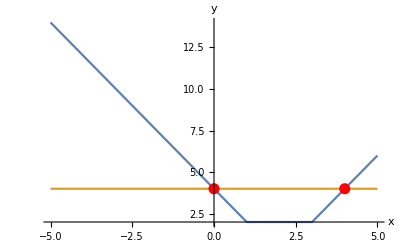

```mathematica
Plot[{f[x],4},{x,-5,5},AxesLabel->{"x","y"},Epilog->{PointSize[0.02],Red,Point[{{x1,f[x1]},{x2,f[x2]}}]}]
```

Problemet är nu löst. Vi har ritat upp ekvationen |x-1|+|x-3| samt lösningen y=4. Vi ser grafiskt att det finns två lösningar.

## Uppgift 3

### Finn lösningen till ekvationen z^7=2-i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.